# EIT with 3-Level Ladder System

```mathematica
Clear["Global`*"]
den = {{r11,r12,r13},{r21,r22,r23},{r31,r32,r33}};
s[x_,y_]:=SparseArray[{{x,y}->1,{Mod[(x +1),3,1],Mod[( y+1),3,1]}-> 0,{Mod[(x +2),3,1],Mod[( y+2),3,1]}-> 0}];

For[i=1,i<4,i++,
For[j=1,j<4,j++,Subscript[γ,i,j]=0]
];
Subscript[γ,2,1]=t21;
Subscript[γ,3,2]=t32;

L[i_,j_]:=Subscript[γ,i,j] (2 s[j,i].den.s[i,j]-s[i,i].den-den.s[i,i]);
Lsum=SparseArray[{{3,3}-> 0}];
For[i=1,i<4,i++,
For[j=1,j<4,j++,Lsum+= L[i,j]]
];
Hnr=1/2{{0,Ωp',0},{Ωp,-2 dp,Ωc'},{0,Ωc,-2(dp+dc)}};
dequation =-I(Hnr.den-den.Hnr)+Lsum//FullSimplify;
dequation//MatrixForm
```

(1/2 ⅈ (-4 ⅈ r22 t21+r12 Ωp-r21 Ωp') | -r12 t21-1/2 ⅈ (2 dp r12-r13 Ωc+(-r11+r22) Ωp') | -1/2 ⅈ (2 r13 (dc+dp-ⅈ t32)-r12 Ωc'+r23 Ωp')
1/2 ⅈ (2 dp r21+2 ⅈ r21 t21-r11 Ωp+r22 Ωp-r31 Ωc') | -1/2 ⅈ (-4 ⅈ r22 t21+4 ⅈ r33 t32-r23 Ωc+r12 Ωp+r32 Ωc'-r21 Ωp') | -1/2 ⅈ (2 dc r23-2 ⅈ r23 (t21+t32)+r13 Ωp+(-r22+r33) Ωc')
1/2 ⅈ (2 r31 (dc+dp+ⅈ t32)-r21 Ωc+r32 Ωp) | 1/2 ⅈ (2 dc r32+2 ⅈ r32 (t21+t32)+(-r22+r33) Ωc+r31 Ωp') | -1/2 ⅈ (-4 ⅈ r33 t32+r23 Ωc-r32 Ωc'))

## Case-A Two Level System

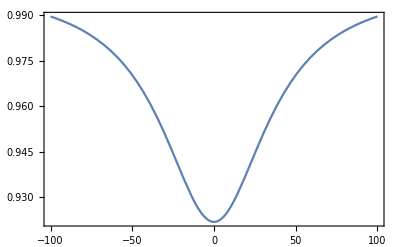

```mathematica
t21=2*π*6.07;
t32=2*π*0.0011;
Ωp=2*π;
Ωc=0;
dc=0;
Hnr=1/2{{0,Ωp,0},{Ωp,-2 dp,Ωc},{0,Ωc,-2(dp+dc)}};
dequation =-I(Hnr.den-den.Hnr)+Lsum;
eqn=Flatten[dequation]//FullSimplify;
eqn1={eqn[[1;;-2]],r11+r22+r33}//Flatten;
Solve[eqn1== {0,0,0,0,0,0,0,0,1},{r11,r12,r13,r21,r22,r23,r31,r32,r33}]//FullSimplify;
Plot[Exp[Im[r21/.%]],{dp,-100,100},Frame-> True]
```

## Case-B Three-Level System EIT Regime

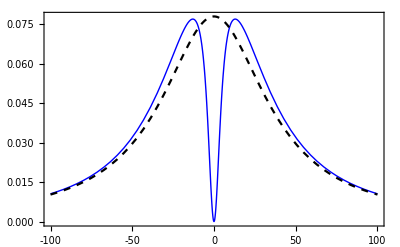

```mathematica
Ωp=2*π;
Ωc=2 π*4;
dc=0;
Hnr=1/2{{0,Ωp,0},{Ωp,-2 dp,Ωc},{0,Ωc,-2(dp+dc)}};
dequation =-I(Hnr.den-den.Hnr)+Lsum;
eqn=Flatten[dequation]//FullSimplify;
eqn1={eqn[[1;;-2]],r11+r22+r33}//Flatten;
Solve[eqn1== {0,0,0,0,0,0,0,0,1},{r11,r12,r13,r21,r22,r23,r31,r32,r33}]//FullSimplify;
Plot[{1-Exp[Im[r21/.%]],1-Exp[Im[r21/.%63]]},{dp,-100,100}, Frame->True , FrameTicks->{{None},{{-100,-50,0,50,100},None}},Axes->{True,False}, PlotStyle->{{Blue,Thick}, {Black,Dashed}} ]
```

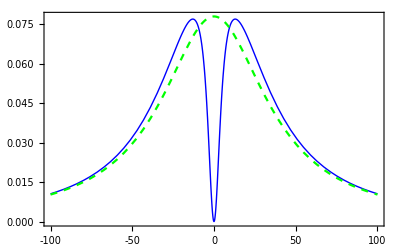

-Graphics-

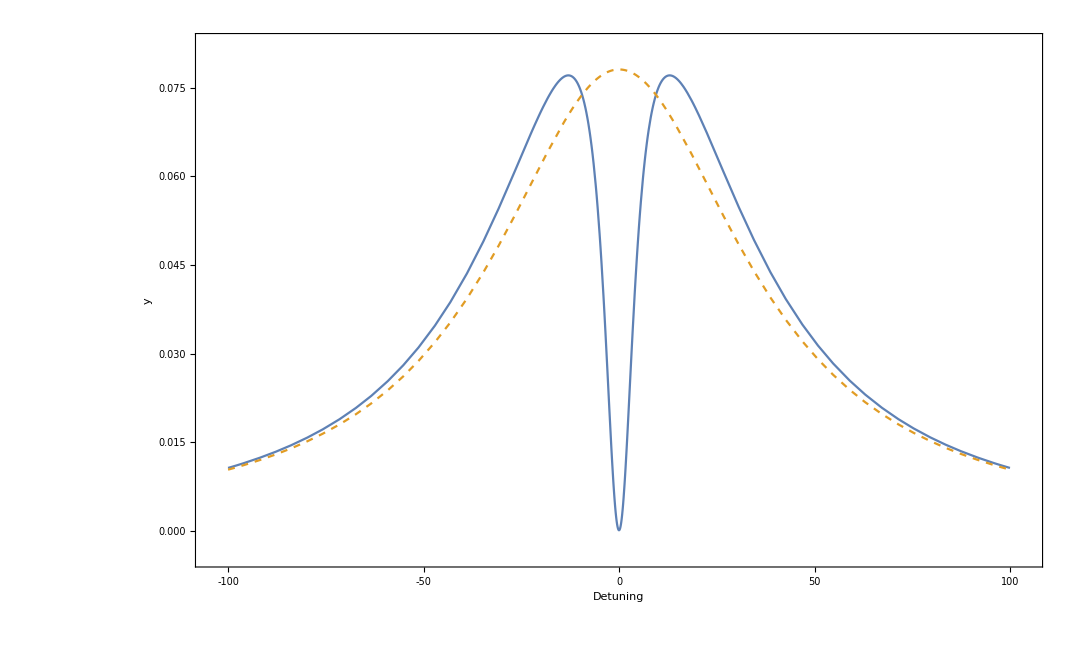
```mathematica
-Graphics-
Export["EIT.png",Plot[{1-Exp[Im[r21/.%]],1-Exp[Im[r21/.%32]]},{dp,-100,100}, Frame->True , FrameTicks->{{None},{{-100,-50,0,50,100},None}},Axes->{True,False}, PlotStyle->{Automatic, Dashed} ]]
```

## Case-C Three Level System AT-Regime

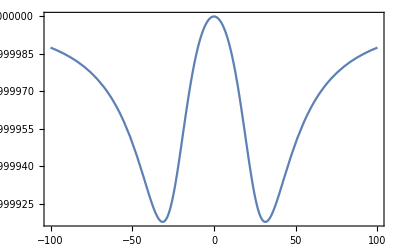

```mathematica
Ωp=2*π* 0.001;
Ωc=20 π;
dc=0;
Hnr=1/2{{0,Ωp,0},{Ωp,-2 dp,Ωc},{0,Ωc,-2(dp+dc)}};
dequation =-I(Hnr.den-den.Hnr)+Lsum;
eqn=Flatten[dequation]//FullSimplify;
eqn1={eqn[[1;;-2]],r11+r22+r33}//Flatten;
Solve[eqn1== {0,0,0,0,0,0,0,0,1},{r11,r12,r13,r21,r22,r23,r31,r32,r33}]//FullSimplify;
Plot[Exp[Im[r21/.%]],{dp,-100,100},Frame-> True]
```